1-2 Sin[1]

1-2 Cos[x]

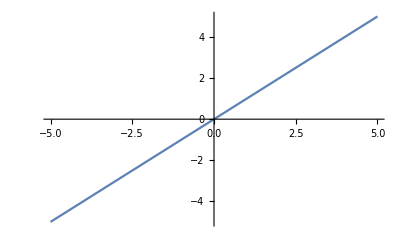

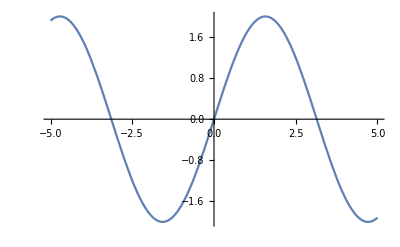

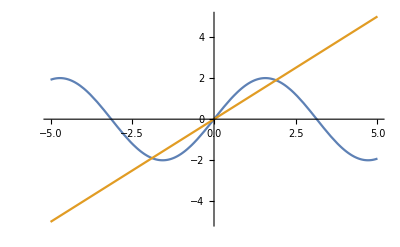

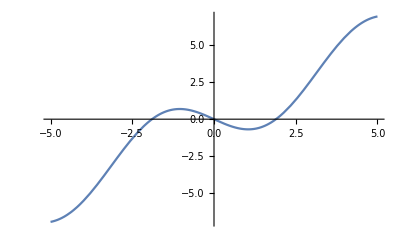

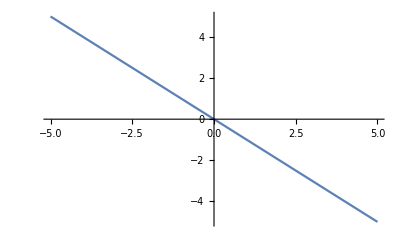

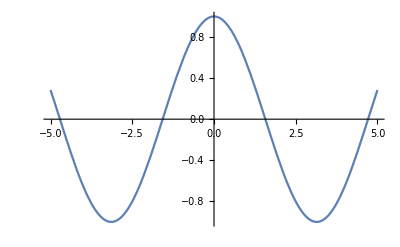

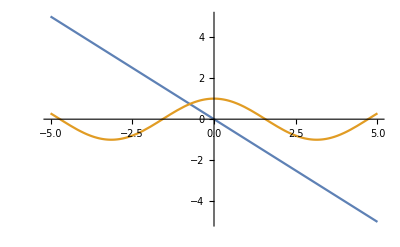

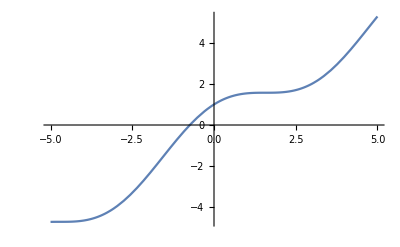

```mathematica
ClearAll[f,f1,x]
f[x_]:=x-2Sin[x]
f[1]
f1[x_]=D[f[x],x]
f2[x_]:=x
f3[x_]:=2Sin[x]
Plot[f2[x],{x,-5,5}]
Plot[f3[x],{x,-5,5}]
Plot[{f3[x],f2[x]},{x,-5,5}]
Plot[x-2*Sin[x],{x,-5,5}]
Plot[-x,{x,-5,5}]
Plot[Cos[x],{x,-5,5}]
Plot[{-x,Cos[x]},{x,-5,5}]
Plot[Cos[x]+x,{x,-5,5}]

Plot[{2Sin[x],x,x-2Sin[x]},{x,-5,5},PlotStyle->{Orange,Dashed,Green},Filling->Axis]
```